```mathematica
(*Initialize Parameters*)
omega0=1300000000;
gamma=0.04;
num=60000;
(*Generate Microphonics*)
delOmega=3;
delOmegaList=RandomVariate[NormalDistribution[0,delOmega],num];
(*delOmegaList={1.8337842711923844,-3.2127185478345153,-2.7215946296524027,-2.070423561410095,-1.9511946642040152,0.03199215069208021};*)

(*Evolution Equations for Each Interval*)
```

```mathematica
x[t_,x0_,v0_,t0_,delOmega_]:=Exp[-gamma*t/2]*(x0*Cos[(omega0+delOmega)*t]+v0/omega0*Sin[(omega0+delOmega)*t])+Exp[-I*omega0*(t+t0)]/(omega0*(2*delOmega-I*gamma))*(1-Exp[-gamma*t/2]*Exp[-I*delOmega*t]);
v[t_,x0_,v0_,t0_,delOmega_]:=Exp[-gamma*t/2]*(-(omega0+delOmega)*x0*Sin[(omega0+delOmega)*t]+(omega0+delOmega)/omega0*v0*Cos[(omega0+delOmega)*t])-I*Exp[-I*omega0*(t+t0)]/(2*delOmega-I*gamma)*(1-Exp[-gamma*t/2]*Exp[-I*delOmega*t]);
(*For Loop below simulates the system behavior over arbitrary lengths of time. The loop produces a list of amplitudes and velocities for "num" number of intervals, using the specific jitter sequence (delOmegaList) above, with each time interval spanning "tjit" number of seconds*)
For[i=0;tjit=0.03;xBCList={0};vBCList={0},i<num,i++,AppendTo[xBCList,x[tjit,xBCList[[i+1]],vBCList[[i+1]],i*tjit,delOmegaList[[i+1]]]];AppendTo[vBCList,v[tjit,xBCList[[i+1]],vBCList[[i+1]],i*tjit,delOmegaList[[i+1]]]]];
```

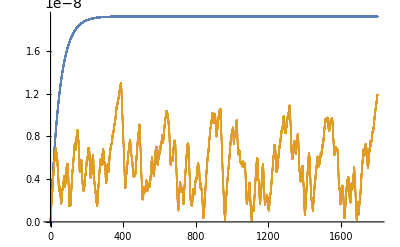

2.1265×10^-11

2.21756×10^-12

0.104282

```mathematica
(*func[t_]:=Piecewise[Table[{x[t-(i-1)*tjit,xBCList[[i]],vBCList[[i]],(i-1)*tjit,delOmegaList[[i]]],(i-1)*tjit<t<i*tjit},{i,1,num}]]*)

(*Converts List Produced above into Plottable Data (Mod(x) vs time plots)*)
xOnBCPlotData=Thread[{Table[i*tjit,{i,0,num}],Table[x[t,0,0,0,0],{t,0,num*tjit,tjit}]}];
BCPlotData=Thread[{Table[i*tjit,{i,0,num}],xBCList}];
ListPlot[{Abs[xOnBCPlotData],Abs[BCPlotData]}]
(*Plot[{Re[x[t,0,0,0,0]],Re[func[t]]},{t,0,num*tjit}, PlotRange -> All]*)
(*Plot[{Abs[x[t,0,0,0,0]],Abs[func[t]]},{t,0,num*tjit}, PlotRange -> All]*)
(*Plot[{Re[func[t]]},{t,0,num*tjit}]*)

(*Compute Power Suppression Factor*)
PowerWOMicrophonics=Sum[(Abs[xOnBCPlotData[[i,2]]])^2,{i,num+1}]
PowerWMicrophonics=Sum[(Abs[BCPlotData[[i,2]]])^2,{i,num+1}]
PowerSuppression=PowerWMicrophonics/PowerWOMicrophonics
```

```mathematica
(*SystemPowerWMicrophonics=NIntegrate[Re[func[t]]^2,{t,0.9999*num*tjit,num*tjit}]
SystemPowerWOMicrophonics=NIntegrate[Re[x[t,0,0,0,0]]^2,{t,0.9999*num*tjit,num*tjit}]
PowerSuppression=SystemPowerWMicrophonics/SystemPowerWOMicrophonics*)
```